# Kane-Mele Model - Floquet

## DOI : 10.1103/PhysRevLett .95 .146802 DOI : 10.1103/PhysRevLett .95 .226801 DOI: https://doi.org/10.1103/PhysRevB.102.201105 Supplemental Material

### 0. 调用

```mathematica
(*仅修改当前笔记本的Input单元样式*)SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Input"],CellFrame->{{2,0},{0,0}},Background->LightBlue]}]]
```

```mathematica
LaunchKernels[10(*8*)];
Needs["TBMethod`"]
ParallelNeeds["TBMethod`"]
StringTemplate["TBMethod<*\"`\"*>`1`<*\"`\"*>*"] /@ {"MDConstruct","EigenSpect", "LGFF", "DataVisualization"};
Scan[Echo@*Information][%]
```

### 1. lattice

注意⚠️：一号元胞周围只包围了一半，因此使用带有反向跃迁的HBloch函数而不是HBlochFull

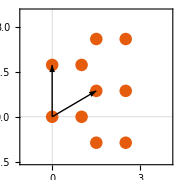

```mathematica
Clear[a,unicell,vasbasis,vas,pts,pts0,pts1,basisArrows]
a=Sqrt[3];
unicell={{0,0},{1,0}};
vasbasis={{3/2,Sqrt[3]/2},{0,Sqrt[3]}};
vas={{0,0},{1,0},{0,1},{1,1},{1,-1}}.vasbasis;

pts=Module[{pts0=Thread[-1{1,-1}->unicell]},<|#->MapAt[TranslationTransform[#],pts0,{All,2}]&/@vas|>];

pts0=Flatten[Values@pts,1];pts1=Flatten[Values@Values@pts,1];
basisArrows=Graphics[{Arrowheads[0.02],Arrow[{{0,0},vasbasis[[1]]}],Arrow[{{0,0},vasbasis[[2]]}]}];
Show[ListPlot[pts1,PlotRange->{{-1,4},{-1.5,3.5}},AspectRatio->1,PlotStyle->PointSize[0.05],ImageSize->Small],basisArrows]
```

### 2. tFunction

```mathematica
Clear[tFunc]
tFunc[{A0_,Avecn_,ω_},mnup_][t_,λSO_,λR_,λv_][inf_->ptf_,ini_->pti_]:=Module[{vd=ptf-pti,d,ϕ,x,y,ξ,fills,sign,conds,Amax,zero=1.*^-5,fu,photonblocks,theta},
d=Norm[vd];{x,y}=Norm/@TakeDrop[vd,1];
photonblocks=(*photonBlocks*)PhotonBlocks[{A0,Avecn,ω},mnup][ptf,pti];
conds={
d<zero,
d> zero &&Abs[d]<1.01,
d>zero&&Abs[d]>Sqrt[3]-0.01&&Abs[d]<Sqrt[3]+0.01};(*参数分别对应的条件*)
	fills={
Hold[ini*λv*PauliMatrix[0]],
Hold[{-t,ⅈ*λR*y,-ⅈ*λR*x}.PauliMatrix[{0,1,2}]],
Hold[theta=ArcTan@@{x,y};ⅈ*λSO*PauliMatrix[3]*ini*(-1)^Quotient[theta,π/3]]};(*条件对应的取值*)
PhotonDress[FillWithCondition[fills,conds],photonblocks]
];
```

```mathematica
tFunc[{1,{2Cos[#],Sin[#]}&,10},1][#t,#λSO,#λR,#λv][pts0[[1]],pts0[[2]]]&[parameters]
```

{{-0.223891+0. ⅈ,0.+0.576725 ⅈ,0.352834+0. ⅈ,-0.0111945+0. ⅈ,0.+0.0288362 ⅈ,0.0176417+0. ⅈ},{0.+0.576725 ⅈ,-0.223891+0. ⅈ,0.+0.576725 ⅈ,0.+0.0288362 ⅈ,-0.0111945+0. ⅈ,0.+0.0288362 ⅈ},{0.352834+0. ⅈ,0.+0.576725 ⅈ,-0.223891+0. ⅈ,0.0176417+0. ⅈ,0.+0.0288362 ⅈ,-0.0111945+0. ⅈ},{0.0111945+0. ⅈ,0.-0.0288362 ⅈ,-0.0176417+0. ⅈ,-0.223891+0. ⅈ,0.+0.576725 ⅈ,0.352834+0. ⅈ},{0.-0.0288362 ⅈ,0.0111945+0. ⅈ,0.-0.0288362 ⅈ,0.+0.576725 ⅈ,-0.223891+0. ⅈ,0.+0.576725 ⅈ},{-0.0176417+0. ⅈ,0.-0.0288362 ⅈ,0.0111945+0. ⅈ,0.352834+0. ⅈ,0.+0.576725 ⅈ,-0.223891+0. ⅈ}}

```mathematica
parameters=Join[<|"λSO"->0.06 #t,"λR"->0.05 #t,"λv"->0.1,"ω"->10,"dup"->1.01,"A0"->0.5,"mnup"->1,"θ"->1.0|>&[#],#]&[<|"t"->1.|>];

tFunc[{1,{2 Cos[#],Sin[#]}&,10},1][#t,#λSO,#λR,#λv][pts0[[1]],pts0[[2]]]&[parameters]
```

{{-0.223891+0. ⅈ,0.+0.576725 ⅈ,0.352834+0. ⅈ,-0.0111945+0. ⅈ,0.+0.0288362 ⅈ,0.0176417+0. ⅈ},{0.+0.576725 ⅈ,-0.223891+0. ⅈ,0.+0.576725 ⅈ,0.+0.0288362 ⅈ,-0.0111945+0. ⅈ,0.+0.0288362 ⅈ},{0.352834+0. ⅈ,0.+0.576725 ⅈ,-0.223891+0. ⅈ,0.0176417+0. ⅈ,0.+0.0288362 ⅈ,-0.0111945+0. ⅈ},{0.0111945+0. ⅈ,0.-0.0288362 ⅈ,-0.0176417+0. ⅈ,-0.223891+0. ⅈ,0.+0.576725 ⅈ,0.352834+0. ⅈ},{0.-0.0288362 ⅈ,0.0111945+0. ⅈ,0.-0.0288362 ⅈ,0.+0.576725 ⅈ,-0.223891+0. ⅈ,0.+0.576725 ⅈ},{-0.0176417+0. ⅈ,0.-0.0288362 ⅈ,0.0111945+0. ⅈ,0.352834+0. ⅈ,0.+0.576725 ⅈ,-0.223891+0. ⅈ}}

```mathematica
(*parameters=Join[<|
"theta"->π,
"λSO"->0.06#t,
"λR"->0.05#t,
"λv"->0.1,
"ω"->10,
"dup"->1.01,
"A0"->0.5,
"mnup"->1
|>&[#],#]&[<|"t"->1.|>]
tFunc[{1,{2Cos[#],Sin[#]}&,10},1][#t,#λSO,#λR,#λv][pts0[[1]],pts0[[2]]]&[parameters]*)
```

### 3. Hamiltonian

```mathematica
(*Clear[params]
params={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01,q->1,Ax->1,Ay->1,ξ1->0.1,ξ2->0.1,ω->15};*)
```

```mathematica
ParallelHMatrixFromHoppings[[{pts[[1]],#1},tFunc[{#A0,{2 Cos[#],Sin[#]}&,#ω},#mnup][#t,#λSO,#λR,#λv][pts0[[1]],pts0[[2]]],#dup]&[parameters][#1]&/@pts]
```

Syntax::bktmop: 表达式 "ParallelHMatrixFromHoppings[{pts[[1]],#1},tFunc[{1,{2Cos[#],Sin[#]}&,10},1][#t,#λSO,#λR,#λv][pts0[[1]],pts0[[2]]],#dup]&[parameters][#1]&/@pts]" 没有前面的 "[".

```mathematica
(hkm=ParallelHMatrixFromHoppings[{pts[[1]],#1},tFunc[{#A0,{2Cos[#],Sin[#]}&,#ω},#mnup][#t,#λSO,#λR,#λv],#dup]&[parameters][#1]&/@pts)//AbsoluteTiming
```

{0.000081,<|{0,0}→ParallelHMatrixFromHoppings[{{-1→{0,0},1→{1,0}},<|λSO→0.06,λR→0.05,λv→0.1,ω→10,dup→1.01,A0→0.5,mnup→1,t→1.|>},tFunc[{0.5,{2 Cos[#1],Sin[#1]}&,10},1][1.,0.06,0.05,0.1],1.01][{-1→{0,0},1→{1,0}}],{3/2,(√3)/2}→ParallelHMatrixFromHoppings[{{-1→{0,0},1→{1,0}},<|λSO→0.06,λR→0.05,λv→0.1,ω→10,dup→1.01,A0→0.5,mnup→1,t→1.|>},tFunc[{0.5,{2 Cos[#1],Sin[#1]}&,10},1][1.,0.06,0.05,0.1],1.01][{-1→{3/2,(√3)/2},1→{5/2,(√3)/2}}],{0,√3}→ParallelHMatrixFromHoppings[{{-1→{0,0},1→{1,0}},<|λSO→0.06,λR→0.05,λv→0.1,ω→10,dup→1.01,A0→0.5,mnup→1,t→1.|>},tFunc[{0.5,{2 Cos[#1],Sin[#1]}&,10},1][1.,0.06,0.05,0.1],1.01][{-1→{0,√3},1→{1,√3}}],{3/2,(3 √3)/2}→ParallelHMatrixFromHoppings[{{-1→{0,0},1→{1,0}},<|λSO→0.06,λR→0.05,λv→0.1,ω→10,dup→1.01,A0→0.5,mnup→1,t→1.|>},tFunc[{0.5,{2 Cos[#1],Sin[#1]}&,10},1][1.,0.06,0.05,0.1],1.01][{-1→{3/2,(3 √3)/2},1→{5/2,(3 √3)/2}}],{3/2,-(√3)/2}→ParallelHMatrixFromHoppings[{{-1→{0,0},1→{1,0}},<|λSO→0.06,λR→0.05,λv→0.1,ω→10,dup→1.01,A0→0.5,mnup→1,t→1.|>},tFunc[{0.5,{2 Cos[#1],Sin[#1]}&,10},1][1.,0.06,0.05,0.1],1.01][{-1→{3/2,-(√3)/2},1→{5/2,-(√3)/2}}]|>}

```mathematica
(*Clear[params]
params={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01,q->1,Ax->1,Ay->-1,ξ1->0.1,ξ2->0.1,ω->6};*)(*Print[Style[Row[{"t=",t/.params,",λSO=",λSO/.params,",λR=",λR/.params,",λv=",λv/.params,",Ax=",Ax/.params,",Ay=",Ay/.params,",ξ1=",ξ1/.params,",ξ2=",ξ2/.params,",ω=",ω/.params}],FontSize->16]]*)
(hkm=ParallelHMatrixFromHoppings[{pts[[1]],#},tFunc[{1,{2Cos[#],Sin[#]}&,10},1][#t,#λSO,#λR,#λv][pts0[[1]],pts0[[2]]],#dup]&/@pts)&[parameters]//AbsoluteTiming
(hkmflo=ParallelHMatrixFromHoppings[{pts[[1]],#},tFuncFlo[t,λSO,λR,λv,{Ax,Ay},{ξ1,ξ2},ω]/.params,dup/.params]&/@pts)//AbsoluteTiming
hBlochkm2D[{kx_,ky_}]:=HBloch[{kx,ky},hkm];
hBloch2D[{kx_,ky_}]:=HBloch[{kx,ky},hkmflo];
```

t=1,λSO=0.06,λR=0.05,λv=0.1,Ax=1,Ay=-1,ξ1=0.1,ξ2=0.1,ω=6

{0.049615,<|{0,0}→SparseArray[…],{3/2,(√3)/2}→SparseArray[…],{0,√3}→SparseArray[…],{3/2,(3 √3)/2}→SparseArray[…],{3/2,-(√3)/2}→SparseArray[…]|>}

{0.079118,<|{0,0}→SparseArray[…],{3/2,(√3)/2}→SparseArray[…],{0,√3}→SparseArray[…],{3/2,(3 √3)/2}→SparseArray[…],{3/2,-(√3)/2}→SparseArray[…]|>}

### 4. FirstBrillouinZone and Path

```mathematica
Clear[loopfbz]
vbsbasis=ReciprocalVectors[vasbasis];
fig1=FirstBrillouinZonePlot[vbsbasis];
r1=vasbasis[[1]];
r2=vasbasis[[2]];
loopfbz=Module[{Γ,X,Y,Z,n=1000},
{Γ,X,Y,Z}={{0,0},{2/3,1/3},{0.5,0.5},{1/3,2/3}(*,{0,0.5}*)}.Take[vbsbasis,2,2]//N;
PathSample[{Γ,X,Y,Z,Γ},n]
];
fig2=ListPlot[loopfbz[[1]],AspectRatio->Automatic,PlotMarkers->"○"];
Show[fig1,fig2]
```

-Graphics-

### 5. Band data and Plot

#### 5.1 Kane-Mele Plot

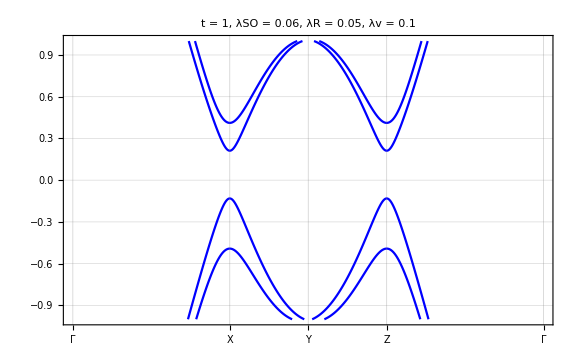
-Graphics-Kane-Mele Model

```mathematica
Clear[banddata]
banddatakm=ParallelBandData[hBlochkm2D,loopfbz[[1]],Method->"Direct"];
Labeled[BandPlot[banddatakm,{"Γ","X","Y","Z","Γ"},loopfbz[[2]],PlotRange->1{-1,1},AspectRatio->1/GoldenRatio,PlotLabel->Style[Row[{"t = ",t/. params,", λSO = ",λSO/. params,", λR = ",λR/. params,", λv = ",λv/. params}],15,FontFamily->"Times New Roman",Italic],ImageSize->Large],Style["Kane-Mele Model",15,FontFamily->"Times New Roman",Italic],Bottom]
```

#### 5.2 Kane-Mele Floquet Plot

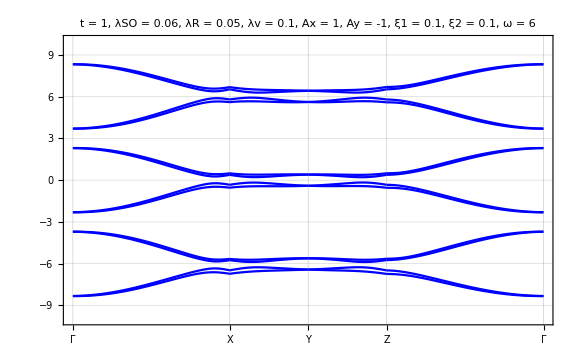
-Graphics-Kane-Mele Model with light

```mathematica
Clear[banddata]
banddata=ParallelBandData[hBloch2D,loopfbz[[1]],Method->"Direct"];
Labeled[BandPlot[banddata,{"Γ","X","Y","Z","Γ"},loopfbz[[2]],PlotRange->(*Automatic*)10{-1,1}(*{-21,-20}*),AspectRatio->1/GoldenRatio,PlotLabel->Style[Row[{"t = ",t/.params,", λSO = ",λSO/.params,", λR = ",λR/.params,", λv = ",λv/.params, ", Ax = ",Ax/.params, ", Ay = ",Ay/.params, ", ξ1 = ",ξ1/.params, ", ξ2 = ",ξ2/.params,", ω = ",ω/.params}],15,FontFamily->"Times New Roman",Italic],ImageSize->Large],Style["Kane-Mele Model with light",15,FontFamily->"Times New Roman",Italic],Bottom]
```

注意⚠️：正确的图像应该是原先的能带上下平移

#### 5.3 Floquet quick check

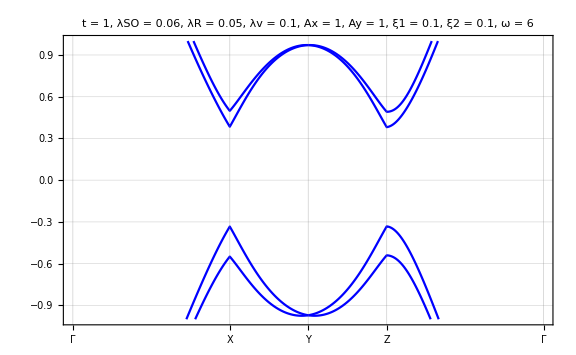
-Graphics-Kane-Mele Model with light

```mathematica
Clear[params]
params={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01,q->1,Ax->1,Ay->1,ξ1->0.1,ξ2->0.1,ω->6};
(hkmflo=ParallelHMatrixFromHoppings[{pts[[1]],#},tFuncFlo[t,λSO,λR,λv,{Ax,Ay},{ξ1,ξ2},ω]/.params,dup/.params]&/@pts)//AbsoluteTiming;
hBloch2D[{kx_,ky_}]:=HBloch[{kx,ky},hkmflo];Clear[banddata]
banddata=ParallelBandData[hBloch2D,loopfbz[[1]],Method->"Direct"];
Labeled[BandPlot[banddata,{"Γ","X","Y","Z","Γ"},loopfbz[[2]],PlotRange->(*Automatic*)1{-1,1}(*{-21,-20}*),AspectRatio->1/GoldenRatio,PlotLabel->Style[Row[{"t = ",t/.params,", λSO = ",λSO/.params,", λR = ",λR/.params,", λv = ",λv/.params, ", Ax = ",Ax/.params, ", Ay = ",Ay/.params, ", ξ1 = ",ξ1/.params, ", ξ2 = ",ξ2/.params,", ω = ",ω/.params}],15,FontFamily->"Times New Roman",Italic],ImageSize->Large],Style["Kane-Mele Model with light",15,FontFamily->"Times New Roman",Italic],Bottom]
```

### 6. WCC(Not fixed)

```mathematica
(fbzsamplingsforWcc2=ParallelogramCartesianSample[vbsbasis,{500,100}];)//AbsoluteTiming;
(wccdata=WannierChargeCenterByWilsonLoop[hBloch2D,#,2]&~ParallelMap~fbzsamplingsforWcc2;)//AbsoluteTiming;
ListPlot[wccdataᵀ,PlotRange->{-1,1}1.2,GridLines->{Automatic,{-1,0,1}},PlotStyle->Blue,FrameLabel->{k,"WCC/π"},FrameTicks->{None,Automatic},PlotMarkers->"O"]
```

### 7. Edge(Not fixed)

#### a. Lattice

```mathematica
crystStruct1Dy[n_]:=Module[{basis0,atombasis,vRs={{0,0},{0,1},{0,-1}},centerize=TranslationTransform[-Mean[#]][#]&},basis0=Thread[-1{-1,1,-1,1}->{{0,0},{1/2,Sqrt[3]/2},{3/2,Sqrt[3]/2},{2,0}}];
atombasis=Join@@CrystalStructure[vasbasisedge,basis0,Tuples[{Range[-n,n],{0}}]];
CrystalStructure[vasbasis,Nest[Delete[{{-1},{-4}}],atombasis,1 0],vRs]]
```

```mathematica
n=3;
vasbasisedge={{3,0},{0,√3}};
CrystalStructurePlot[{2 n,1} vasbasisedge,crystStruct1Dy[n],AspectRatio->Automatic,PlotStyle->PointSize[0.02],PlotRange->All,PlotRangePadding->{Scaled[.1],Scaled[.1]},ImageSize->Full](*For check use*)
```

```mathematica
Clear[cryststruct1dy,n]
n=(*50*)20(*4*);
cryststruct1dy=crystStruct1Dy[n];
```

#### b. Hamiltonian

```mathematica
(*计算哈密顿量和hbloch*)
Clear[t,t2,λSO,λv,λR,dup]
(*params2={t->1,λSO->0.06,λR->0.05,λv->0.4,dup->Sqrt[3]+0.01};*)
hkmedge=ParallelHMatrixFromHoppings[{cryststruct1dy[[1]],#},tFuncFlo[t,λSO,λR,λv,{Ax,Ay},{ξ1,ξ2},ω]/.params,dup/. params]&/@cryststruct1dy
hBloch1Dy[ky_]:=HBlochFull[{0,ky},hkmedge]
(*!这里注意"hBloch1Dy[ky_] := HBlochFull[{0, ky}, h01km]"中是"HBlochFull"而不是"HBloch"
！当晶格周围被完全包围之后使用HBlochFull
！当晶格周围没有被完全包围使用HBloch，会自动补全。*)
```

#### c. Band data and Plot

```mathematica
eup = 0.25 4; kn = 200 4; kgrid =  Subdivide[##, kn] & @@ ({-2, 0} π/√3);
(banddata1dy = 
    ParallelBandData[hBloch1Dy, kgrid, 
     Method ->(*"Direct"*)"Banded"];) // AbsoluteTiming
BandPlot[Select[AnyTrue[Between[{-1, 1} eup]]][banddata1dy], {OverBar["Y"], OverBar["Γ"], OverBar["Y"]},  Insert[MinMax[kgrid], Mean[kgrid], 2], DataRange -> MinMax[kgrid], AspectRatio ->(*1.7*)0.7(*/GoldenRatio*), PlotRange ->{-1, 1} eup,PlotStyle -> Directive[(*Thin,*)Blue],ImageSize->Large]
```

#### f. Quick Check for Edge State

```mathematica
Clear[t,t2,λSO,λv,λR,dup]
params2={t->1,λSO->0.06,λR->0.05,λv->0.1,dup->Sqrt[3]+0.01};
hkmedge=ParallelHMatrixFromHoppings[{cryststruct1dy[[1]],#},tFuncFlo[t,λSO,λR,λv,{Ax,Ay},{ξ1,ξ2},ω]/.params,dup/. params2]&/@cryststruct1dy;
hBloch1Dy[ky_]:=HBlochFull[{0,ky},hkmedge]
(banddata1dy = 
    ParallelBandData[hBloch1Dy, kgrid, 
     Method ->(*"Direct"*)"Banded"];) // AbsoluteTiming;
BandPlot[Select[AnyTrue[Between[{-1, 1} eup]]][banddata1dy], {"0", "π", "2π"},(*{OverBar["Y"], OverBar["Γ"], OverBar["Y"]},*)  Insert[MinMax[kgrid], Mean[kgrid], 2], DataRange -> MinMax[kgrid], AspectRatio ->(*1.7*)0.7(*/GoldenRatio*), PlotRange ->{-1, 1} eup,PlotStyle -> Directive[(*Thin,*)Blue],ImageSize->Large,PlotLabel->Style[Row[{"t = ",t/.params2,", λSO = ",λSO/.params2,", λR = ",λR/.params2,", λv = ",λv/.params2,}],22,FontFamily->"Times New Roman",Italic]]
```